## Classification with K Nearest Neighbours (KNN)

## The method

The K nearest neighbour (KNN) is probably the simplest classifier one can imagine. 
The method assumes that points that are close to one another are similar.
In order to measure the similarity between data points, the method requires some notion of distance, d.
The method can be applied to data characterised by any number M of features

Algorithm:

The method starts with a set of N already-classified data.

Given a new, unclassified data point,

Measure the distance to all the classified data points

Look at the K points with the smallest distance

Assign the unclassified point to the class having the largest number of points nearby.

### Example: Data from two classes with M = 2 features

#### The data

```mathematica
class1={{2.0375,2.17342},{3.26311,2.91653},{2.12867,1.64643},{2.97427,0.949959},{2.98993,2.51624},{3.91724,1.95322},{2.78868,2.62858},{3.70735,2.169},{2.74074,1.53303},{4.40572,3.10587},{3.055,2.34357},{4.47329,1.69863},{3.40663,2.3143},{3.99787,1.62153},{3.81106,2.73322},{4.17481,2.35417},{3.87181,3.00465},{3.48454,2.13469},{3.48324,2.70445},{3.47954,2.14079},{3.91258,1.39807},{2.96974,3.04991},{3.23336,1.9782},{3.82975,2.44744},{3.10847,2.70287}};
class2={{2.33026,3.21666},{1.16294,2.87106},{0.54208,4.16626},{1.47782,3.07471},{1.56869,3.27184},{3.37085,4.08707},{2.36088,2.68858},{1.98111,2.70751},{2.63036,2.29086},{0.378934,2.45828},{1.87487,3.7792},{2.64598,2.06865},{2.37989,2.85652},{1.35068,3.21348},{2.53051,2.75737},{1.94521,1.19612},{2.54625,2.32219},{1.41766,2.47492},{2.06653,2.60251},{3.2109,2.57492},{3.10848,4.10173},{2.14416,2.58644},{2.11392,3.44677},{1.66484,2.9603},{2.74075,4.04955},{1.55977,3.18465},{2.15189,3.2445},{1.71115,3.02909},{2.52201,3.17202},{3.0048,4.068}};
```

Aside: This is just a particular realisation of multinormal random variables.

Class 1: N_1 = 25 data points from a multivariate normal x~ N(μ_1,Σ_1) with μ_1 = {3.5,2} and  Σ_1={{σ,0},{0,σ}} where σ=0.3
Class 2: N_2 = 30 data points from a multivariate normal x~ N(μ_2,Σ_2) with μ_2 = {2,3} and  Σ_2={{σ,0},{0,σ}} where σ=0.5

```mathematica
gaussian[μ_,σ_,n_]:=RandomVariate[MultinormalDistribution[μ,{{σ,0},{0,σ}}],n];
cluster1=gaussian[{3.5,2},0.3,25];
cluster2=gaussian[{2,3},0.5,30];
```

```mathematica
Length[class1]
```

25

```mathematica
Length[class2]
```

30

Anyway, let us focus on the data {class1,class2} looks like this on a scatterplot:

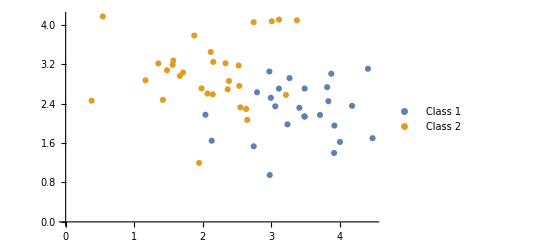

```mathematica
ListPlot[{class1,class2},PlotLegends->{"Class 1","Class 2"}]
```

Let’s now consider an example whose class is unknown:

```mathematica
unknown={2.7,2.5};
```

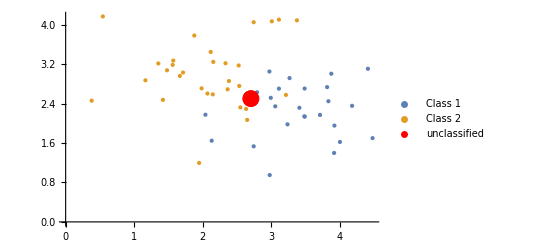

```mathematica
Show[ListPlot[{class1,class2},PlotStyle->PointSize[Large],PlotLegends->{"Class 1","Class 2"}],ListPlot[{unknown},PlotStyle->{Red,PointSize[0.03]},PlotLegends->{"unclassified"}]]
```

Here, the unclassified point looks closer to a point in class 1. For k=1 we would conclude that the unclassified point belongs to class 1. 

Euclidean distance:
Here, the Euclidean distance between points would be a suitable metric to assess the distance between data points. For two points with coordinates P_1:(x_1,y_1) and P_2:(x_2,y_2), the Euclidean distance is (remember Pythagoras theorem?):

d(P_1,P_2)=√((x_1-x_2)^2+(y_1-y_2)^2)

The Euclidean distance can be easily calculated in Mathematica with the function EuclideanDistance

#### Train a classifier

Train a classifier using the data for the two classes with KNN:

```mathematica
k=3;
c=Classify[<|"class 1"->class1,"class 2"->class2|>,Method->{"NearestNeighbors","NeighborsNumber"->k}]
```

ClassifierFunction[…]

Note that we specify Method →  “NearestNeighbors” to force the classifier to use the KNN method

#### Results

The predicted class for the unclassified point considered above

```mathematica
c[unknown]
```

class 2

We can look at the predicted classification for many points in the region [0,5]x[0,5]

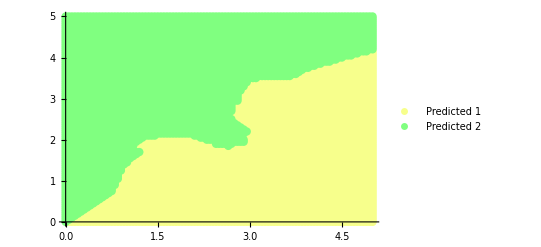

```mathematica
line=Range[0,5,0.05];
points=Tuples[line,2];
pred=c[points];
temp=Tally[Sort[pred]];
ListPlot[{points[[Ordering[pred]]][[1;;temp[[1,2]]]],points[[Ordering[pred]]][[temp[[1,2]]+1;;Length[pred]]]}, PlotStyle->{{RGBColor[0.97,1.,0.55],PointSize[0.015]},{RGBColor[0.5,1,0.5],PointSize[0.015]}},PlotLegends->{"Predicted 1","Predicted 2"}]
```

Plotting the training data together with the predictions, it looks like the predictions make sense.

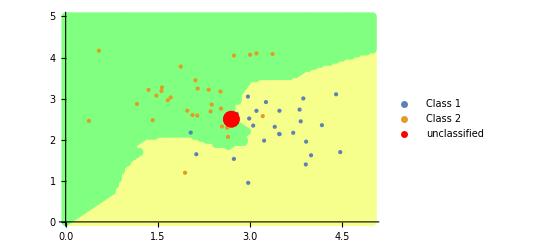

```mathematica
Show[ListPlot[{points[[Ordering[pred]]][[1;;temp[[1,2]]]],points[[Ordering[pred]]][[temp[[1,2]]+1;;Length[pred]]]},PlotStyle->{{RGBColor[0.97,1.,0.55],PointSize[0.015]},{RGBColor[0.5,1,0.5],PointSize[0.015]}}],ListPlot[{class1,class2},PlotStyle->PointSize[Large], PlotLegends->{"Class 1","Class 2"}],ListPlot[{unknown},PlotStyle->{Red,PointSize[0.03]}, PlotLegends->{"unclassified"}]]
```

Each predicted value carries a probability

```mathematica
c[unknown,"Probabilities"]
```

<|class 1→0.350877,class 2→0.649123|>

```mathematica
predProb=c[points,"Probability"-> "class 1"];
```

The probability to be blue (class 1) can be plotted as follows:

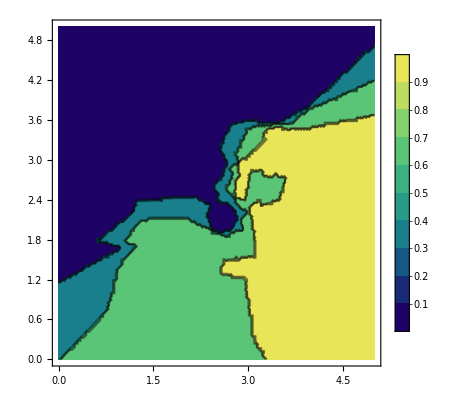

```mathematica
ContourPlot[c[{x,y},"Probability"-> "class 1"],{x,0,5},{y,0,5},ColorFunction->"BlueGreenYellow",PlotLegends->Automatic]
```

#### Task for you

Task 1. Above, we have used the function Classify to implement the KNN algorithm. However, the KNN is simple enough as for you to try and implement it from scratch. In Mathematica, this mostly reduces to list manipulation. You may find the function DistanceMatrix useful for this task.

#### Choosing K - What is the most appropriate value of K?

In order to test what is the best value of k, let us assume that we have a test dataset consisting of 100 points in each of the classes used to train the classifier.

```mathematica
test1={{3.69765,2.425},{4.00246,1.7043},{3.67851,2.35709},{3.09471,2.38492},{4.35489,1.92649},{2.49695,2.0163},{3.14867,2.36211},{3.2053,2.68336},{4.20344,1.77836},{3.85341,1.76304},{4.53586,1.70389},{3.9201,2.2827},{3.75888,1.18488},{2.58984,2.9361},{3.13904,1.73358},{3.29348,1.94813},{3.38422,1.71062},{4.07289,1.32853},{3.61245,2.31473},{3.38784,3.48309},{3.587,1.88643},{3.58562,1.72929},{2.86693,2.39598},{4.01831,2.08565},{2.76329,1.76006},{3.08565,2.24786},{3.5749,1.99016},{3.73692,1.46203},{3.11591,0.699028},{3.19433,1.7758},{4.26733,2.46615},{4.40833,1.63886},{4.49667,2.17903},{3.15713,2.36502},{4.46839,1.83373},{3.95766,2.00865},{4.07501,2.17388},{4.23976,2.20229},{3.66269,2.33798},{3.55418,1.46151},{3.87515,2.10868},{4.16764,1.20674},{3.3876,1.59848},{3.28385,1.37589},{4.04836,3.16752},{3.85173,1.62781},{3.40901,2.04648},{4.52642,2.43679},{2.82829,1.22172},{3.18796,2.0057},{3.1485,1.96313},{3.36805,2.05351},{4.38693,2.56164},{3.97995,2.10409},{3.10401,1.80086},{4.31875,2.41585},{4.3487,2.15989},{3.59251,1.33439},{2.66569,2.0487},{3.92473,2.50061},{2.85013,2.10431},{3.40472,2.47447},{2.76985,2.69663},{3.44683,1.6691},{3.17166,0.958893},{3.79293,1.07948},{3.98053,1.86416},{3.82835,2.27272},{3.60706,2.67779},{3.48554,2.23264},{3.68985,2.61655},{4.49082,2.93306},{3.81977,2.70466},{3.87071,1.82603},{4.16702,1.66934},{3.17651,1.80516},{2.71918,3.12922},{3.4963,1.0366},{4.28098,2.13197},{3.22015,1.39214},{4.40256,2.03617},{3.69581,1.52117},{3.41103,0.478234},{3.45423,2.04626},{4.26757,2.3529},{3.13664,1.79897},{3.55487,0.959028},{3.61446,1.67961},{3.71712,3.42464},{3.81838,1.99846},{3.55068,1.41219},{3.58602,1.79908},{3.9541,2.13226},{3.30767,1.28242},{2.41843,2.31907},{2.90847,2.72472},{3.64148,3.13154},{3.37644,2.52048},{3.98562,2.96588},{2.75177,1.39729}};
```

```mathematica
test2={{0.95687,2.69517},{2.12336,2.55889},{3.2428,3.73901},{2.00587,2.69546},{3.4121,2.5474},{2.92513,3.774},{2.56104,2.51773},{2.11118,3.14264},{2.4376,3.88499},{0.795899,3.68845},{1.41006,4.6006},{1.11538,2.58179},{1.91973,2.40091},{1.83767,2.83101},{3.00397,3.96719},{1.53329,1.97645},{0.695639,3.81913},{2.21648,3.42582},{1.71273,3.8465},{3.63061,2.84921},{2.09371,2.29577},{3.09598,3.23855},{2.28146,2.81962},{1.3963,3.48191},{1.61762,3.31309},{1.215,3.18326},{1.89351,2.0016},{3.49676,2.50121},{3.4541,2.97602},{1.80406,3.10423},{1.16029,3.91063},{1.39922,3.22763},{2.10658,3.40985},{0.844508,3.43312},{2.62814,2.83561},{1.63139,4.22504},{0.925671,3.19173},{2.34651,3.74065},{2.12083,1.95229},{1.58269,3.02092},{1.5437,2.02666},{1.76961,3.66388},{2.30519,2.9204},{3.08037,1.85724},{1.90292,1.71796},{1.71724,3.0693},{2.10508,2.98762},{1.60397,2.66963},{1.08091,3.46818},{2.03748,1.25679},{2.77493,2.89056},{0.853442,3.22942},{2.79002,2.72923},{2.17492,2.60946},{0.604566,3.9165},{3.51097,3.96328},{1.87673,3.67857},{1.83145,2.73943},{2.38053,3.37201},{3.88259,3.37853},{2.07748,3.31165},{1.63759,3.71683},{2.54581,3.2266},{2.30963,3.45482},{2.36608,3.52711},{1.60499,1.9101},{2.23342,3.30305},{2.42768,3.65616},{1.35252,3.38105},{3.47429,1.46866},{3.10386,3.49016},{2.95303,3.91402},{3.13311,2.99702},{2.30861,2.39949},{1.31052,3.67139},{2.66398,3.04728},{1.04975,3.17411},{2.6292,3.63219},{1.61728,2.75131},{1.9627,4.09016},{2.90663,3.75383},{1.69621,4.02906},{3.26184,3.85506},{2.78579,3.38213},{2.38153,2.06138},{2.07109,3.27966},{1.00052,3.07841},{3.25323,1.78738},{1.15535,3.38155},{1.96551,2.94941},{1.16575,3.00169},{1.31604,2.51537},{2.32501,2.19729},{2.3489,3.74024},{2.05063,3.67617},{3.59505,4.56855},{2.28931,3.70004},{2.83931,3.3759},{1.3859,2.80713},{1.17835,2.6751}};
```

It is interesting to visually check that training and test datasets seem to be similar. For instance, for class 1, one obtains:

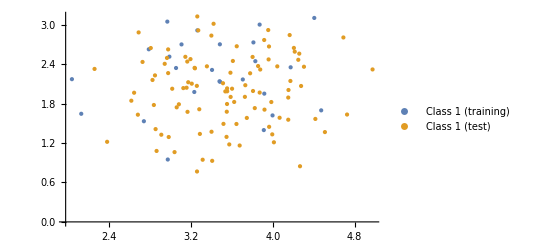

```mathematica
ListPlot[{class1,test1},PlotStyle->{PointSize[Medium]},PlotLegends->{"Class 1 (training)","Class 1 (test)"}]
```

We then define the test dataset as follows:

```mathematica
testset=<|"class 1"-> test1,"class 2"-> test2|>;
```

We create a module to plot the predicted class and test class for any value of k

```mathematica
plotTest[k0_]:=Module[{k=k0,line,points,ctemp,pred,temp},
line=Range[0,5,0.05];
points=Tuples[line,2];ctemp=Classify[<|"class 1"->class1,"class 2"->class2|>,Method->{"NearestNeighbors","NeighborsNumber"->k}];
pred=ctemp[points];
temp=Tally[Sort[pred]];
Show[ListPlot[{points[[Ordering[pred]]][[1;;temp[[1,2]]]],points[[Ordering[pred]]][[temp[[1,2]]+1;;Length[pred]]]},PlotStyle->{{RGBColor[0.97,1.,0.55],PointSize[0.015]},{RGBColor[0.5,1,0.5],PointSize[0.015]}},PlotLabel->"k="<>ToString[k]],ListPlot[{test1,test2},PlotStyle->PointSize[Medium], PlotLegends->{"Test 1","Test 2"}]]
]
```

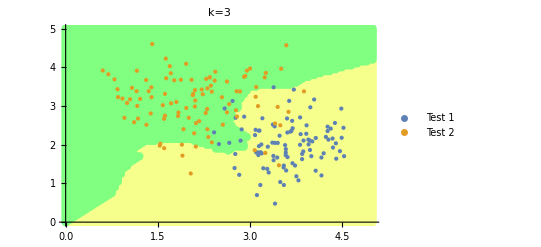

```mathematica
plotTest[3]
```

Let us compare the test data and predicted classification for several values of k

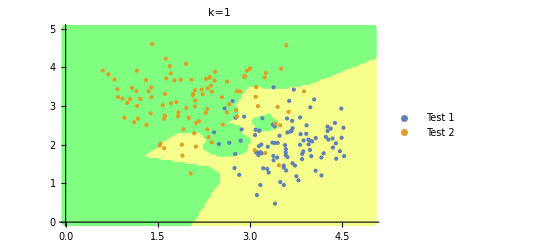
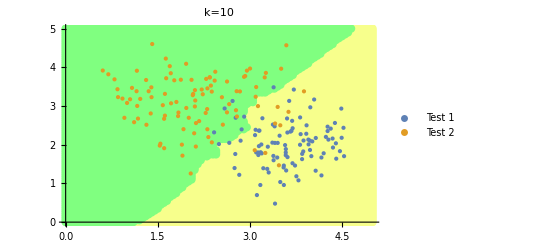
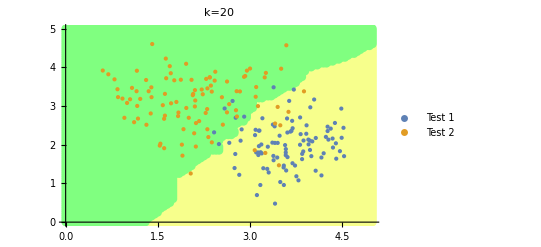
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
TableForm[{{plotTest[1],plotTest[3]},{plotTest[10],plotTest[20]}},{plotTest[30],plotTest[49]}]
```

Remarks:

For k = 1, the prediction regions are complicated since we only look at the nearest neighbour.

The model is complicated: It changes a lot as we move around because the nearest neighbours change a lot.

The classifier fits very well the data but it is not generic in the sense that it will typically not predict well the class of new data.

The model is simpler for larger values of k: The nearest neighbours do not change so much as we classify new samples.

In the extreme case in which k=N_1+N_2 (i.e. we use as many neighbours as data points), the prediction would be identical for any new sample. Bad...

```mathematica
Length[class1]
```

25

```mathematica
Length[class2]
```

30

The compromise must be for some intermediate value of k.

#### Using a ClassifierMeasurements object

In order to look at the effect of k in a more systematic way, we obtain a ClassifierMeasurements object and study performance measures.

We first train a classifier for a certain value of k

```mathematica
k=1;
c=Classify[<|"class 1"->class1,"class 2"->class2|>,Method->{"NearestNeighbors","NeighborsNumber"->k}]
```

ClassifierFunction[…]

and then obtain the corresponding ClassifierMeasurements object:

```mathematica
cm=ClassifierMeasurements[c,testset]
```

ClassifierMeasurementsObject[…]

We can obtain the misclassification error for a given value of k:

```mathematica
cm["Error"]
```

0.135

In order to systematically check the error for several values of k, it is useful to write a function:

```mathematica
error[k0_,class1in_,class2in_,testsetin_]:=Module[{k=k0,ctemp,class1=class1in,class2=class2in,cm,testset=testsetin},
ctemp=Classify[<|"class 1"->class1,"class 2"->class2|>,Method->{"NearestNeighbors","NeighborsNumber"->k}];
cm=ClassifierMeasurements[ctemp,testset];
cm["Error"]
]
```

```mathematica
error[1,class1,class2,testset]
```

0.135

Once we have a function for the error for a given value of k, it is easy to see how the error changes with k. Here is a plot of the error as a function of k:

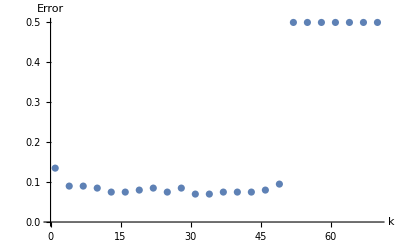

```mathematica
ListPlot[Table[{k,error[k,class1,class2,testset]},{k,1,70,3}],PlotRange->All,AxesLabel->{"k","Error"}]
```

#### Problems for skewed data

What happens for k⩾50? 

This can be investigated in terms of the confusion matrix. We just write a function for this analogous to the error[k] function written above:

```mathematica
confusion[k0_,class1in_,class2in_,testsetin_]:=Module[{k=k0,ctemp,class1=class1in,class2=class2in,cm,testset=testsetin},
ctemp=Classify[<|"class 1"->class1,"class 2"->class2|>,Method->{"NearestNeighbors","NeighborsNumber"->k}];
cm=ClassifierMeasurements[ctemp,testset];
cm["ConfusionMatrixPlot"]
]
```

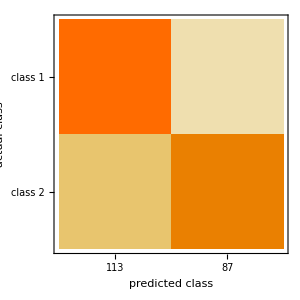

```mathematica
confusion[1,class1,class2,testset]
```

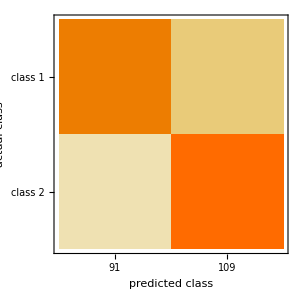
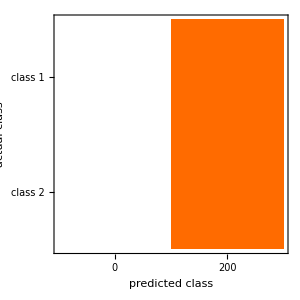
k=1
-Graphics- | k=49
-Graphics-
k=50
-Graphics- | k=100
-Graphics-

```mathematica
TableForm[{{{"k=1",confusion[1,class1,class2,testset]},{"k=49",confusion[49,class1,class2,testset]}},{{"k=50",confusion[50,class1,class2,testset]},{"k=100",confusion[100,class1,class2,testset]}}}]
```

For k⩾50, all points are assigned to class 2. What is the reason?

This is because there are more points in the training data for class 2 than for class 1 (remember, N_1=25 and N_2=30). As a result, when the number of nearest neighbours considered is large enough, class 2 will dominate simply because there are more points in the training data.

Conclusion: The exact value of k for which problems appear depends on the specific data used for training and testing. However, the KNN will normally be problematic for large k when using skewed training data.

## Data normalisation (or standardization)

Methods based on distances between features require some standardization of the data. Distances are highly dependent on how features are measured. In fact, if some features take values much larger than other, distances are dominated by the features taking the largest values.

Imagine, for instance, that we characterise three people by {salary,number of children}

```mathematica
people={{12000,2},{10000,8},{12000,8}};
```

The Euclidean distance between pairs of individuals in this dataset is:

```mathematica
N[DistanceMatrix[people]]//MatrixForm
```

(0. | 2000.01 | 6.
2000.01 | 0. | 2000.
6. | 2000. | 0.)

The distance is ~2000 between the first and second individuals but it is just 6 between the first and third individuals. The huge difference in distances is mostly dictated by the salary difference; the number of children does not count much.

In order to make sure that features with small values significantly count towards distances, it is often useful to normalise each feature in a way that all of them have the same relative contribution to the distance.

There are several ways to normalise the data. Two popular choices are:

Min-max normalisation: The following transformation is applied to each feature, x

x'=(x-Min(x))/(Max(x)-Min(x))

Obviously, all normalised features are x'∈[0,1]

Standardization:

x'=(x-Mean(x))/(StandardDeviation(x))

### Normalisation with Wolfram Language

Normalisation can be easily implemented in Wolfram Language with the function Standardize.

#### Standardization

Standardize[list] applies standardization to the elements of the list

It is easy to see the effect in the following example:

```mathematica
x={1,7,3,2,6,7};
y=Standardize[x]
```

{-5 √(10/159),4 √(10/159),-2 √(10/159),-7 √(5/318),5 √(5/318),4 √(10/159)}

```mathematica
N[y]
```

{-1.25392,1.00314,-0.50157,-0.877747,0.626962,1.00314}

```mathematica
StandardDeviation[x]
```

√(106/15)

```mathematica
(x-Mean[x])/StandardDeviation[x]
```

{-5 √(10/159),4 √(10/159),-2 √(10/159),-7 √(5/318),5 √(5/318),4 √(10/159)}

```mathematica
StandardDeviation[y]
```

1

The relative position of the data points is similar in x and y but y is centred around y=0 and has standard deviation 1:

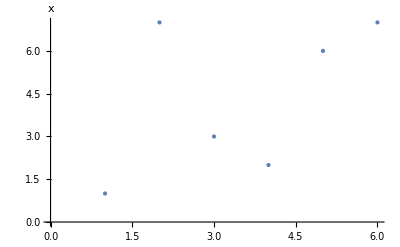
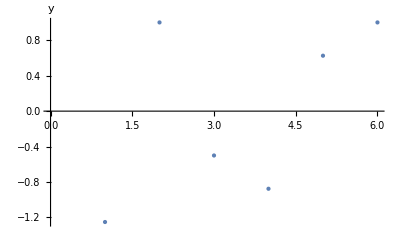

```mathematica
{ListPlot[x,PlotStyle->PointSize[Large],AxesLabel-> "x"],ListPlot[y,PlotStyle->PointSize[Large],AxesLabel-> "y"]}
```

For the example of {salary,number of children} of people, the distances between individuals become more meaningful after normalization (here, I use standardize):

```mathematica
N[DistanceMatrix[Standardize[people]]]//MatrixForm
```

(0. | 2.44949 | 1.73205
2.44949 | 0. | 1.73205
1.73205 | 1.73205 | 0.)

The distance between first-second and first-third are more similar which might make sense, for instance, when calculating an insurance premium for different individuals.

Min-Max normalization

The Standardize function can be implemented in a more general way as follows:

Standardize[list,f_1,f_2] = (list-f_1[list])/f_2[list]

For Min-Max normalization,

```mathematica
f2[x_]:=Max[x]-Min[x];
```

```mathematica
f1[x_]:=Min[x];
```

```mathematica
Standardize[x,f1,f2]
```

{0,1,1/3,1/6,5/6,1}

```mathematica
Standardize[x,Min,f2]
```

{0,1,1/3,1/6,5/6,1}

For standardization, one could do the following:

```mathematica
Standardize[x,Mean,StandardDeviation]
```

{-5 √(10/159),4 √(10/159),-2 √(10/159),-7 √(5/318),5 √(5/318),4 √(10/159)}

Of course, for Min-Max normalization, one could use the formula straight away:

```mathematica
(x-Min[x])/(Max[x]-Min[x])
```

{0,1,1/3,1/6,5/6,1}

For the {salary, number of children} example, using Min-Max normalization gives the following distances:

```mathematica
N[DistanceMatrix[Standardize[people,Min,f2]]]//MatrixForm
```

(0. | 1. | 0.5
1. | 0. | 0.5
0.5 | 0.5 | 0.)

Good news: The superfunction Classify standardizes the data automatically!

One can see this by digging into the classifier function as follows:

```mathematica
c[[1]]
```

<|ExampleNumber→55,ClassNumber→2,Input→<|Preprocessor→ToMLDataset,Processor→  ImputeMissing→Standardize|>,Output→<|Preprocessor→ToMLDataset,Processor→  ToVector→IntegerEncodeNominalVector→FromVector→FirstValues,ProbabilityPostprocessor→Identity,Name→class,Marginal→<|class 1→0.45614,class 2→0.54386|>|>,Prior→Automatic,Utility→SparseArray[…],Threshold→0,TieBreaker→RandomChoice,PerformanceGoal→Automatic,BatchProcessing→Automatic,Model→<|NeighborsFunction→NeighborsFunction[Nearest,...],NeighborsNumber→3,ClassPriors→{0.45614,0.54386},TrainingOutput→NumericArray[…],DistributionSmoothing→0.5,Processor→FirstValues,Method→NearestNeighbors,PostProcessor→Identity,Options→<|NeighborsNumber→<|Value→3,Options→<||>|>,DistributionSmoothing→<|Value→0.5,Options→<||>|>,NearestMethod→<|Value→KDtree,Options→<||>|>|>|>,TrainingInformation→<|PanelCell→7841,TrainingFunction→Classify,EMIterations→Missing[KeyAbsent,EMIterations],ProcessorEntropyShift→0,PreprocessingTime→2.488345,LossName→MeanCrossEntropy,BestModelInformation→,Configurations→,MaxTrainingSize→55,PreprocessorEvaluationTime→0.0000112,PreprocessorMemory→35216,InputDimension→2,OutputDimension→1,BaselineLogProbability→-0.689295,VariableBudget→True,CheckpointingInfo→<|Checkpointing→False|>,UserStop→False,NaturalStop→True,AbortStop→False,LastReportingTime→3.8139311861353805×10^9,RoundPartitioning→|>,AnomalyDetector→None,Log→<|Example→ | Type | Weight | Values
f1 | NumericalVector | 1 | { {⋯_2} }
1 examples | no weights | grouped examples | no density weights |  |  | Dataset[Association[(_String -> _Association)..]],TrainingTime→3.87315,MaxTrainingMemory→25702600,DataMemory→5824,FunctionMemory→107000,LanguageVersion→{12.1,1},Date→Mon 9 Nov 2020 17:19:46GMT,ProcessorCount→4,ProcessorType→x86-64,OperatingSystem→Windows,SystemWordLength→64,Evaluations→{}|>|>

```mathematica
c[[1]]["Input"]
```

<|Preprocessor→ToMLDataset,Processor→  ImputeMissing→Standardize|>

### Checking standardization with synthetic data (check it yourself)

One can check that standardizing the data manually does not lead to a significant improvement when using Classify.

Let us consider a data consisting of two classes. 
In order to avoid skewness, we consider both data

Class 1: N_1 = 30 data points from a multivariate normal x~ N(μ_1,Σ_1) with μ_1 = {35,2} and  Σ_1={{σ,0},{0,σ}} where σ=0.3
Class 2: N_2 = 30 data points from a multivariate normal x~ N(μ_2,Σ_2) with μ_2 = {34,6} and  Σ_2={{σ,0},{0,σ}} where σ=0.3

```mathematica
class1={{36.4224,2.51019},{34.6856,2.48067},{34.8301,1.6967},{35.4655,1.67861},{34.451,2.77757},{35.4332,1.67166},{35.4558,2.65165},{35.0157,2.42548},{35.5285,2.86564},{35.8449,2.71228},{34.5182,1.6843},{34.0726,2.05017},{36.497,1.53132},{35.2942,1.9852},{34.8358,2.15371},{35.6651,1.87923},{34.9283,1.05336},{35.027,1.934},{35.5365,2.10257},{35.8449,2.23236},{34.365,2.09965},{35.4053,2.00093},{33.9597,1.99581},{34.9164,2.71324},{34.4227,2.17086},{34.4874,2.53882},{34.8388,2.41709},{34.664,2.08424},{35.1762,1.82132},{35.2818,0.651869}};
class2={{33.8218,6.20804},{33.8693,5.78748},{33.4125,6.0152},{33.85,6.15595},{34.3405,5.38224},{33.4924,5.90071},{33.6573,6.05925},{34.8603,6.85556},{35.039,6.88862},{34.196,5.45328},{33.9328,5.17409},{34.2066,5.53001},{32.8041,6.28592},{33.8289,6.53645},{33.0744,6.71042},{33.09,4.90156},{34.5952,6.30859},{33.4216,5.27052},{34.12,5.57103},{34.743,5.33922},{33.861,6.30709},{33.9817,6.34217},{34.32,5.38606},{33.4545,5.49808},{34.4093,6.041},{33.3439,6.11982},{33.6095,5.74525},{34.5353,6.08666},{33.4011,7.43094},{33.9707,5.51947}};
```

```mathematica
gaussian[μ_,σ1_,σ2_,n_]:=RandomVariate[MultinormalDistribution[μ,{{σ,0},{0,σ}}],n];
cluster1=gaussian[{3500,2},0.3,30];
cluster2=gaussian[{3499,3},0.3,30];
```

```mathematica
cluster1=RandomVariate[UniformDistribution[{{0,20},{1,3.5}}],50];
cluster2=RandomVariate[UniformDistribution[{{13,33},{1.5,4}}],50];
```

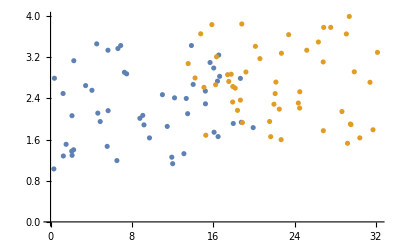

```mathematica
class1=cluster1;
class2=cluster2;
ListPlot[{cluster1,cluster2}]
```

```mathematica
c=Classify[<|"class 1"->class1,"class 2"->class2|>,Method->{"NearestNeighbors"}]
```

ClassifierFunction[…]

```mathematica
test1=RandomVariate[UniformDistribution[{{0,20},{1,3.5}}],50];
test2=RandomVariate[UniformDistribution[{{13,33},{1.5,4}}],50];
testset=<|"class 1"-> test1,"class 2"-> test2|>;
```

```mathematica
cm=ClassifierMeasurements[c,testset]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.85

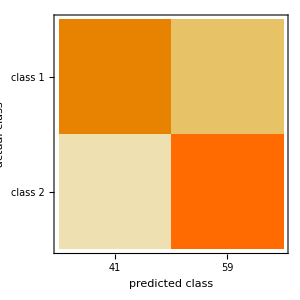

```mathematica
cm["ConfusionMatrixPlot"]
```

Define a normalisation function that will be applied to each feature:

```mathematica
labels1=ConstantArray["class 1",Length[class1]];
labels2=ConstantArray["class 2",Length[class2]];
labels=Join[labels1,labels2];
```

```mathematica
temp1=Standardize[Join[class1,class2][[All,1]]];
temp2=Standardize[Join[class1,class2][[All,2]]];
```

```mathematica
trainingNormData=Table[Flatten[Transpose[{temp1,temp2}][[i]]]-> labels[[i]],{i,1,Length[labels]}];
```

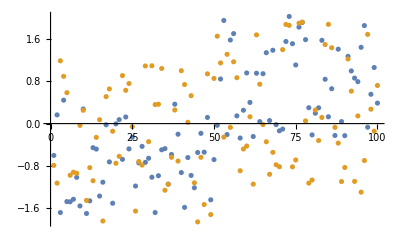

```mathematica
ListPlot[{temp1,temp2}]
```

```mathematica
cfnorm=Classify[trainingNormData,Method->"NearestNeighbors"]
```

ClassifierFunction[…]

```mathematica
temp1=Standardize[Join[class1,class2][[All,1]]];
temp2=Standardize[Join[class1,class2][[All,2]]];
```

```mathematica
labels1=ConstantArray["class 1",Length[test1]];
labels2=ConstantArray["class 2",Length[test2]];
labels=Join[labels1,labels2];
```

```mathematica
testNormData=Table[Flatten[Transpose[{temp1,temp2}][[i]]]-> labels[[i]],{i,1,Length[labels]}];
```

```mathematica
cmnorm=ClassifierMeasurements[cfnorm,testNormData]
```

ClassifierMeasurementsObject[…]

```mathematica
cmnorm["Accuracy"]
```

0.9

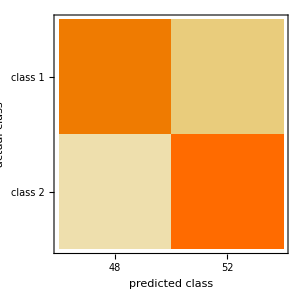

```mathematica
cmnorm["ConfusionMatrixPlot"]
```

## The curse of dimensionality

The KNN quantifies the similarity between data point using distances. As a consequence, its accuracy might degrade as the number of features increases (unless the number of data points increases as well). This is called “curse of dimensionality”. The ultimate reason for this is that if we have few points in a high-dimensional space, the distance of a point to its closest neighbour is not necessarily much smaller than the distance to any other point in the space.

Fortunately, the curse of dimensionality is not very bad in many cases and, in fact, KNN and other machine learning methods based on distances often perform very well with high dimensional data.

### Example

Let us illustrate the phenomenon in a very simple case.

#### 1-dimensional data

Consider two disjoint 1-dimensional datasets for class A and B.

Examples of class A take uniformly distributed random values x∈ [-0.5,-0.01]
Examples of class B take uniformly distributed random values in x∈ [0.01,0.5]

```mathematica
ndata=10;
AD1=RandomVariate[UniformDistribution[{-0.50,-0.01}],ndata];
BD1=RandomVariate[UniformDistribution[{0.01,0.5}],ndata];
```

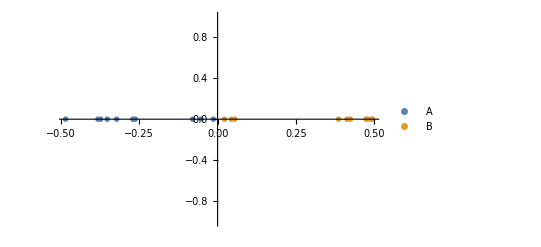

```mathematica
Show[ListPlot[{Transpose[{AD1,Table[0,{i,1,ndata}]}],Transpose[{BD1,Table[0,{i,1,ndata}]}]},PlotMarkers->{"OpenMarkers", Medium},PlotLegends->{"A","B"}]]
```

Let us now add a point whose class is unknown (defined in such a way that it will typically belong to class A):

```mathematica
unknown={-0.03,0};
```

(A 0 is added in the 2nd dimension just for representation.)

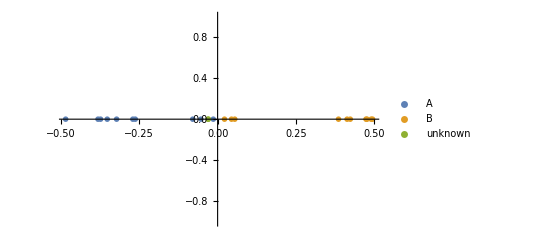

```mathematica
Show[ListPlot[{Transpose[{AD1,Table[0,{i,1,ndata}]}],Transpose[{BD1,Table[0,{i,1,ndata}]}],{unknown}},PlotMarkers->{"OpenMarkers", Medium},PlotLegends->{"A","B","unknown"}]]
```

Let us train a KNN classifier with k = 1 using AD1 and BD1 as training data:

```mathematica
c1D=Classify[<|"A"->AD1,"B"->BD1|>,Method->{"NearestNeighbors","NeighborsNumber"->1,"NearestMethod"-> "Scan"}]
```

ClassifierFunction[…]

We now classify the unknown datum:

```mathematica
c1D[unknown[[1]]]
```

A

#### 2-dimensional data

Let us extend the data to include a 2nd feature, y. 

Examples of class A can take uniformly distributed random values y∈[0,0.7]
Examples of class B can take uniformly distributed random values y∈[0.3,1.0]

Note that the data for the two classes can overlap in the 2nd dimension but one can still see two different clusters.

```mathematica
AD2=Transpose[{AD1,RandomVariate[UniformDistribution[{0,0.7}],ndata]}];
BD2=Transpose[{BD1,RandomVariate[UniformDistribution[{0.3,1.0}],ndata]}];
```

```mathematica
AD2
```

{{-0.352235,0.0368448},{-0.262781,0.260231},{-0.01383,0.402365},{-0.270498,0.361055},{-0.484953,0.428564},{-0.373522,0.356029},{-0.0531279,0.430584},{-0.0793417,0.258403},{-0.381641,0.394313},{-0.322324,0.460336}}

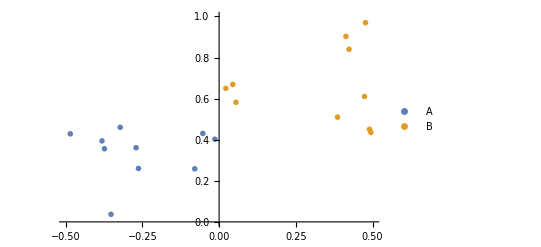

```mathematica
ListPlot[{AD2,BD2},PlotMarkers->{"OpenMarkers", Medium},PlotLegends->{"A","B"},PlotRange->{{-0.5,0.5},{0,1}}]
```

We use the training data to train a KNN classifier with k = 1

```mathematica
c2D=Classify[<|"A"->AD2,"B"->BD2|>,Method->{"NearestNeighbors","NeighborsNumber"->1,"NearestMethod"-> "Scan"}]
```

ClassifierFunction[…]

Unknown example: x=-0.03, y in [0,0.7]

We now test the classification of the unknown point depending on its value of y

```mathematica
Manipulate[TableForm[{ListPlot[{AD2,BD2,{{unknown[[1]],y}}},PlotMarkers->{"OpenMarkers", Medium},PlotLegends->{"A","B"},PlotRange->{{-0.5,0.5},{0,1}}],{"Predicted",c2D[{unknown[[1]],y}]}}],{y,0,0.7}]
```

## Strengths and weaknesses of KNN

Based on its simplicity and typically good performance, KNN is often a first choice for classification.

#### Strengths

Simple and effective

It just uses the data without assuming anything on it.

Fast training phase

#### Weaknesses

Strictly speaking, it is not learning anything. In other words, it does not provide a model which could be used to understand how the features are related to the class.

Requires selection of an appropriate number of neighbours, k

Although the training phase is fast, the classification phase can be slow. Indeed, one has to measure the distance between the new point and all the already-classified points.

As every method based on distance between instances, it suffers from the curse of dimensionality.